```mathematica
note[b_,x0_,t_,v_]:=Module[{a=b},Which[x0=="1",AppendTo[a,SoundNote["C",t,SoundVolume->v]],x0=="2",AppendTo[a,SoundNote["D",t,SoundVolume->v]],x0=="3",AppendTo[a,SoundNote["E",t,SoundVolume->v]],x0=="4",AppendTo[a,SoundNote["F",t,SoundVolume->v]],x0=="5",AppendTo[a,SoundNote["G",t,SoundVolume->v]],x0=="6",AppendTo[a,SoundNote["A",t,SoundVolume->v]],x0=="7",AppendTo[a,SoundNote["B",t,SoundVolume->v]],x0=="0",AppendTo[a,SoundNote[None,t,SoundVolume->v]],x0=="-",a[[-1,2]]*=2,x0=="_",a[[-1,2]]/=2,x0=="*",a[[-1,2]]*=1.5,x0=="t",a[[-1,2]]/=3,x0=="%",a[[-1,2]]/=5,x0==".",a[[-1,1]]=If[NumberQ@ToExpression[StringTake[a[[-1,1]],-1]],StringReplacePart[a[[-1,1]],ToString[ToExpression[StringTake[a[[-1,1]],-1]]-1],-1],StringInsert[a[[-1,1]],"3",-1]],x0=="'",a[[-1,1]]=If[NumberQ@ToExpression[StringTake[a[[-1,1]],-1]],StringReplacePart[a[[-1,1]],ToString[ToExpression[StringTake[a[[-1,1]],-1]]+1],-1],StringInsert[a[[-1,1]],"5",-1]],x0=="#",a[[-1,1]]=StringInsert[a[[-1,1]],"#",-1],x0=="b",a[[-1,1]]=StringInsert[a[[-1,1]],"b",-1]];a];

noteh[b_,x0_]:=Module[{h=b},Which[x0=="1",AppendTo[h,"C"],x0=="2",AppendTo[h,"D"],x0=="3",AppendTo[h,"E"],x0=="4",AppendTo[h,"F"],x0=="5",AppendTo[h,"G"],x0=="6",AppendTo[h,"A"],x0=="7",AppendTo[h,"B"],x0==".",h[[-1]]=If[NumberQ@ToExpression[StringTake[h[[-1]],-1]],StringReplacePart[h[[-1]],ToString[ToExpression[StringTake[h[[-1]],-1]]-1],-1],StringInsert[h[[-1]],"3",-1]],x0=="'",h[[-1]]=If[NumberQ@ToExpression[StringTake[h[[-1]],-1]],StringReplacePart[h[[-1]],ToString[ToExpression[StringTake[h[[-1]],-1]]+1],-1],StringInsert[h[[-1]],"5",-1]],x0=="#",h[[-1]]=StringInsert[h[[-1]],"#",-1],x0=="b",h[[-1]]=StringInsert[h[[-1]],"b",-1]];h];

mf[s_,t_,x_]:=Module[{lh=StringLength[x],xx=x,a={},v=1,par=False,h={},i,x0},For[i=1,i≤lh,i++,x0=StringTake[xx,1];
If[par,If[x0==")",AppendTo[a,SoundNote[h,t,SoundVolume->v]];par=False;
h={},h=noteh[h,x0]],If[x0=="(",par=True,v=Which[x0=="p",0.5,x0=="P",0.2,x0=="m",0.8,x0=="f",1,True,v];a=note[a,x0,t,v]]];
xx=StringDrop[xx,1]];
Sound[Prepend[a,s],{0,Plus@@(#[[2]]&/@a)}]];

(*函数mf[s,t,x]，s，t，x分别为乐器类型、时长单位（秒）、乐谱*)

m[t_,x_]:=mf["Piano",t,x];

(*函数m[t,x]，t，x分别为时长单位（秒）、乐谱，乐器类型默认为钢琴*)

ms[s_,x_]:=mf[s,0.5,x];

(*函数ms[s,x]，s，x分别为乐器类型、乐谱，时长单位默认为0 .5秒*)

m0[x_]:=m[0.5,x];

(*函数m0[x]，x为乐谱，乐器类型默认为钢琴，时长单位默认为0 .5秒*)
```

```mathematica
以上定义了四个自定义函数：函数mf[s,t,x]，s，t，x分别为乐器类型、时长单位 （秒）、乐谱。函数m[t,x]，t，x分别为时长单位 （秒）、乐谱，乐器类型默认为钢琴。函数ms[s,x]，s，x分别为乐器类型、乐谱，时长单位默认为0 .5秒。函数m0[x]，x为乐谱，乐器类型默认为钢琴，时长单位默认为0 .5秒。在Mathematica中输入以上内容，按【Shift】+【Enter】，即可利用以上函数写音乐。乐谱格式为我在我所记得的那一点点简谱的基础上胡编乱造而成：控制音高的符号：1、2、3、4、5、6、7分别表示长度为一个单位的C、D、E、F、G、A、B。
.表示表示前一个音符降低八度。'表示表示前一个音符升高八度。b表示表示前一个音符降低半度

#表示表示前一个音符升高半度。当一个音符后同时带上需要加上#（或b）和'(或.)时，需将#（或b）放在'(或.)前面。同一个音符后不能带多个#、b。控制音长的符号：-表示前一个音符长度增长一个单位。_表示表示前一个音符长度减半。

*表示表示前一个音符长度变为原来的1.5倍。t表示表示前一个音符长度变为原来的三分之一。%表示表示前一个音符长度变为原来的五分之一。控制音强的符号：p表示此后的音强变为0.5（默认音强为1）。P表示此后的音强变为0.2。m表示此后的音强变为0.8。f表示此后的音强变为1。其他符号：0表时长一个单位的休止符（休止符的长度可通过在0后添加控制音长的符号来控制）。
|表示小节线，只是为了阅读方便，可以不写。(表示进入和声状态。)表示退出和声状态。和声的实现：用括号()将几个音符括在其中。括号内有效的字符只有1、2、3、4、5、6、7、0、b、#、'、.这些控制音高的符号。控制音长的符号-、_、*、t、%请添加在括号后面。此外，还可以写成多个声部，然后用Sound[{ , ,}]连接起来。
```

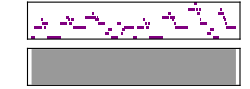

```mathematica
m[0.5,"5.|1*1_3_2_1_2__2__|5.-5.5.|2*2_4_3_2_3__3__|1-11|4*4_5_4_3_4__3__|2-6.7.|5.*5._2_2_6._7.__7.__|1-15.|1*1_3_2_1_2__2__|5.-5.5.|4*4_5_4_3_4__2__|1-11|6*6_1'_6_5_6__3__|2-6.7.|5.*5_6_5_4_3__2__|1-1"]
```

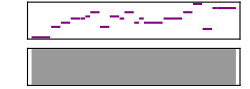

```mathematica
m[0.5,"5.-12|33_4_51|43_52_3_|2-|3-57|7.6_6-"]
```

```mathematica
Sound[SoundNote/@{"C#","D#","E#","F#","G#","A#","B#"},0.5]
```

```mathematica
Sound[SoundNote/@{"C-1","D-1","E-1","F-1","G-1","A-1","B-1","C0","D0","E0","F0","G0","A0","B0","C1","D1","E1","F1","G1","A1","B1","C2","D2","E2","F2","G2","A2","B2","C3","D3","E3","F3","G3","A3","B3","C4","D4","E4","F4","G4","A4","B4","C5","D5","E5","F5","G5","A5","B5","C6","D6","E6","F6","G6","A6","B6","C7","D7","E7","F7","G7","A7","B7","C8","D8","E8","F8","G8","A8","B8","C9","D9","E9","F9","G9"},3]
```

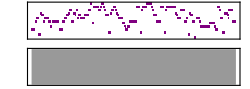

```mathematica
m[0.5,"5.-12|3.4_31|2-16.|1--|5.-12|33_4_51|43_52_3_|3_2_2-|3-57|7.6_6-|55_6_76_5_|3-|4.4_56|54_3_2-|7.7._6._5.6.|1-|1-6-|4.5_6-77_7_76_5_|3-|1-6-|4.5_6-|66_6_64_3_|2-|5-12|3.4_31_1_|2.2_22_1_|6.6.--7.-7.6._|5.652_2_|4.4_43_2_|5-|1-"]
```

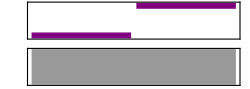

```mathematica
Sound[{SoundNote["G3"],SoundNote["C"]}]
```

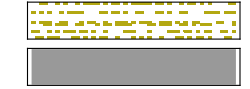

```mathematica
Sound[SoundNote[#,1/6,"Warm"]&/@(Pick[{15,25,9,12,16,21},#,1]&/@CellularAutomaton[30,{{0,0,0,1,1,1},0},13,{50,5}])]
```

```mathematica
ArrayPlot[CellularAutomaton[30,{{1,0,0,0,0,0},0},13,13]]
```

-Graphics-